------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPlain` version 0.0.0-developer, {2024,8,29}

CopyRight © 2023, Will Barker and Sebastian Zell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

/home/williamb/Documents/paper-x

Gravitational wave integration

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e6g", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

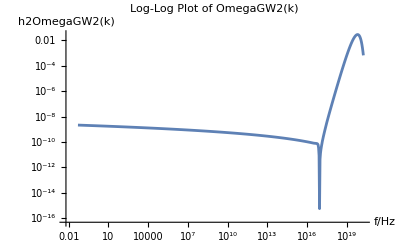

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

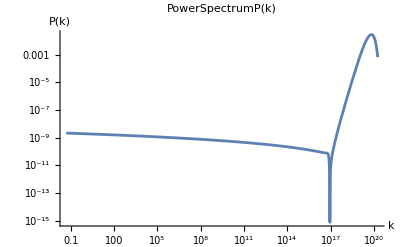

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e6g", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e6g", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

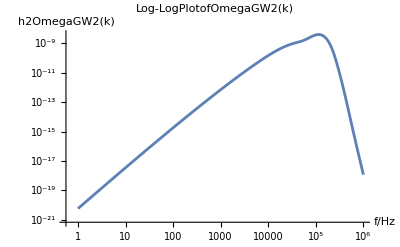

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e6g_lower", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

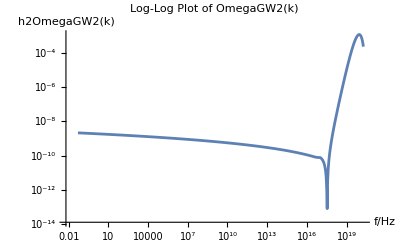

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

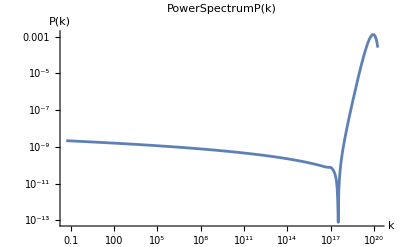

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e6g_lower", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e6g_lower", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

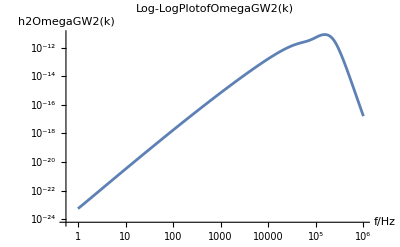

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e6g_upper", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

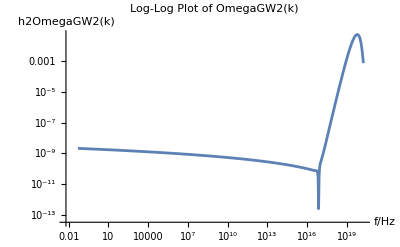

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

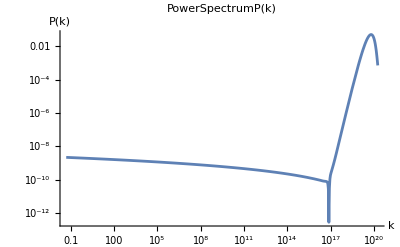

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e6g_upper", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e6g_upper", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

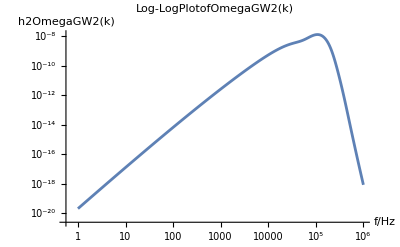

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e7g", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

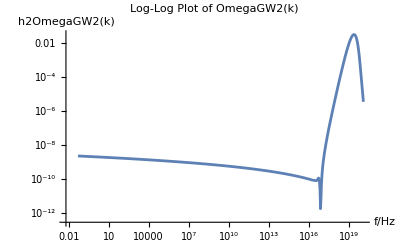

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

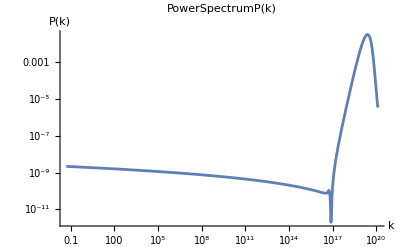

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e7g", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e7g", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

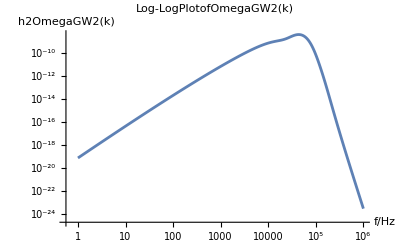

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e7g_lower", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

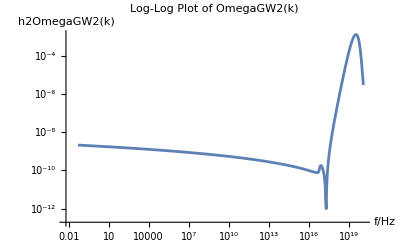

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

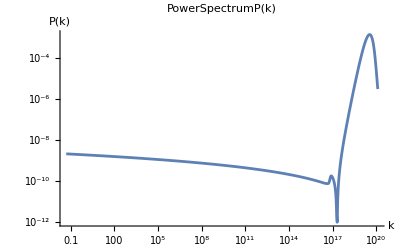

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e7g_lower", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e7g_lower", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

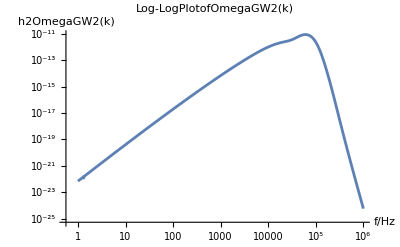

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e7g_upper", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

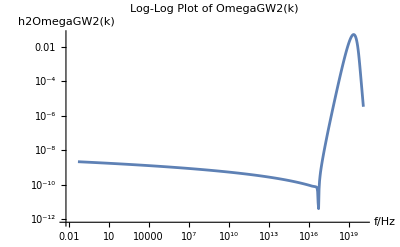

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

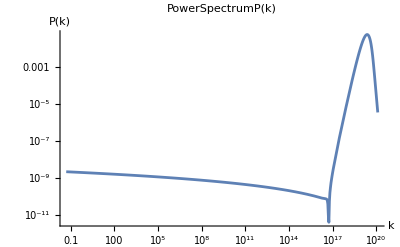

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e7g_upper", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e7g_upper", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

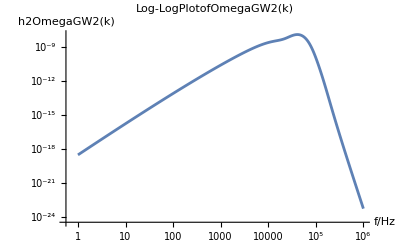

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e8g", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

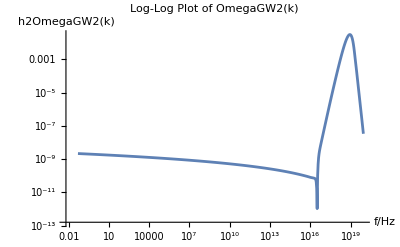

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

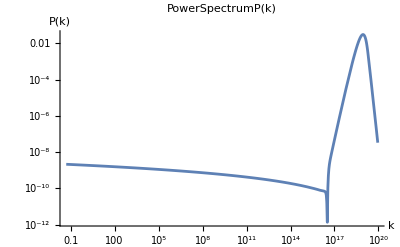

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e8g", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e8g", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

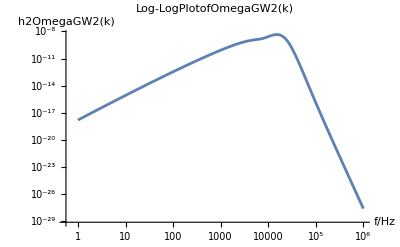

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e8g_lower", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

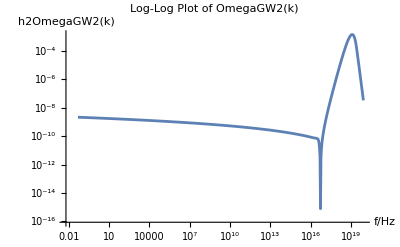

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

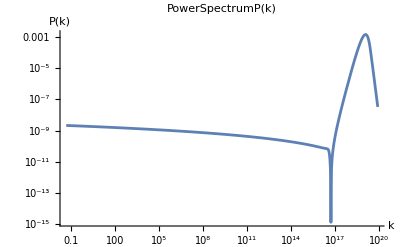

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e8g_lower", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e8g_lower", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

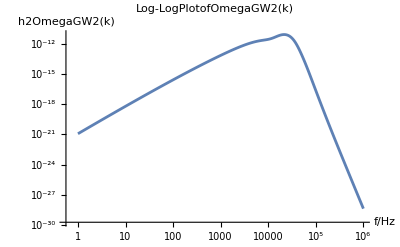

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e8g_upper", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

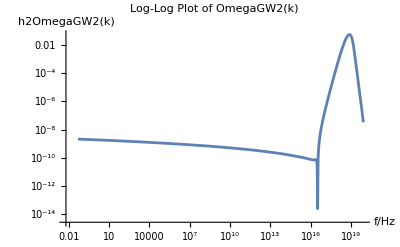

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

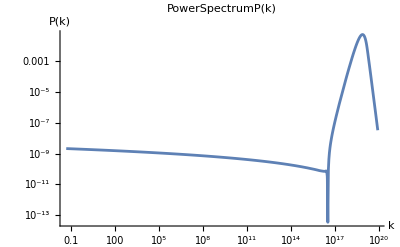

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e8g_upper", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e8g_upper", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

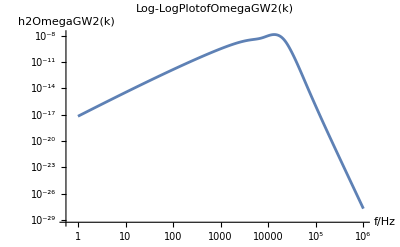

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e9g", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

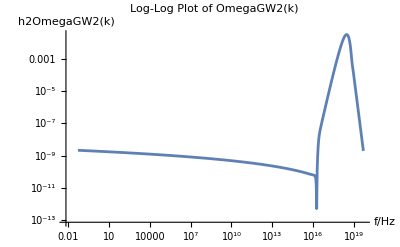

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

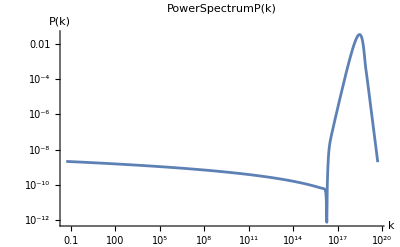

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e9g", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e9g", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

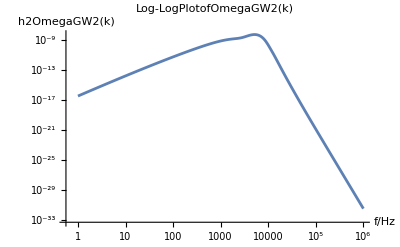

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e9g_lower", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

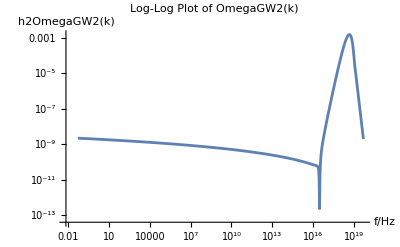

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

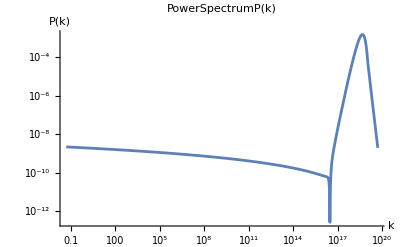

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e9g_lower", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e9g_lower", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

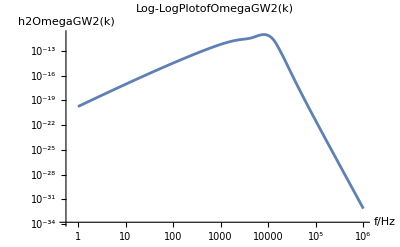

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e9g_upper", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

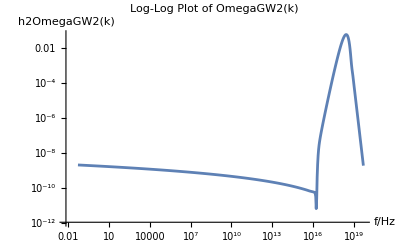

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

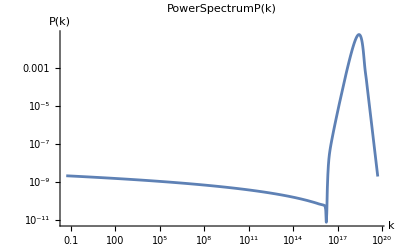

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 1; highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^14,6.55829×10^14,6.64952×10^14,6.74203×10^14,6.83582×10^14,6.93091×10^14,7.02733×10^14,7.12509×10^14,7.22421×10^14,7.32471×10^14,7.42661×10^14,7.52992×10^14,7.63467×10^14,7.74088×10^14,7.84857×10^14,7.95775×10^14,8.06846×10^14,8.1807×10^14,8.29451×10^14,8.40989×10^14,8.52689×10^14,8.64551×10^14,8.76578×10^14,8.88772×10^14,9.01136×10^14,9.13672×10^14,9.26383×10^14,9.3927×10^14,9.52337×10^14,9.65585×10^14,9.79018×10^14,9.92637×10^14,1.00645×10^15,1.02045×10^15,1.03464×10^15,1.04904×10^15,1.06363×10^15,1.07843×10^15,1.09343×10^15,1.10864×10^15,1.12406×10^15,1.1397×10^15,1.15555×10^15,1.17163×10^15,1.18793×10^15,1.20445×10^15,1.22121×10^15,1.2382×10^15,1.25542×10^15,1.27289×10^15,1.2906×10^15,1.30855×10^15,1.32675×10^15,1.34521×10^15,1.36393×10^15,1.3829×10^15,1.40214×10^15,1.42164×10^15,1.44142×10^15,1.46147×10^15,1.4818×10^15,1.50242×10^15,1.52332×10^15,1.54451×10^15,1.566×10^15,1.58778×10^15,1.60987×10^15,1.63226×10^15,1.65497×10^15,1.67799×10^15,1.70134×10^15,1.72501×10^15,1.749×10^15,1.77333×10^15,1.798×10^15,1.82302×10^15,1.84838×10^15,1.87409×10^15,1.90016×10^15,1.9266×10^15,1.9534×10^15,1.98057×10^15,2.00812×10^15,2.03606×10^15,2.06438×10^15,2.0931×10^15,2.12222×10^15,2.15174×10^15,2.18168×10^15,2.21203×10^15,2.2428×10^15,2.274×10^15,2.30563×10^15,2.33771×10^15,2.37023×10^15,2.4032×10^15,2.43664×10^15,2.47053×10^15,2.5049×10^15,2.53975×10^15,2.57508×10^15,2.6109×10^15,2.64722×10^15,2.68405×10^15,2.72139×10^15,2.75925×10^15,2.79763×10^15,2.83655×10^15,2.87601×10^15,2.91602×10^15,2.95659×10^15,2.99772×10^15,3.03942×10^15,3.0817×10^15,3.12457×10^15,3.16804×10^15,3.21211×10^15,3.2568×10^15,3.3021×10^15,3.34804×10^15,3.39461×10^15,3.44184×10^15,3.48972×10^15,3.53827×10^15,3.58749×10^15,3.6374×10^15,3.688×10^15,3.7393×10^15,3.79132×10^15,3.84406×10^15,3.89754×10^15,3.95176×10^15,4.00673×10^15,4.06247×10^15,4.11899×10^15,4.17629×10^15,4.23439×10^15,4.29329×10^15,4.35302×10^15,4.41357×10^15,4.47497×10^15,4.53723×10^15,4.60035×10^15,4.66434×10^15,4.72923×10^15,4.79502×10^15,4.86173×10^15,4.92936×10^15,4.99793×10^15,5.06746×10^15,5.13796×10^15,5.20943×10^15,5.2819×10^15,5.35538×10^15,5.42988×10^15,5.50542×10^15,5.58201×10^15,5.65966×10^15,5.7384×10^15,5.81822×10^15,5.89916×10^15,5.98123×10^15,6.06444×10^15,6.1488×10^15,6.23434×10^15,6.32107×10^15,6.409×10^15,6.49816×10^15,6.58856×10^15,6.68022×10^15,6.77315×10^15,6.86737×10^15,6.96291×10^15,7.05977×10^15,7.15798×10^15,7.25756×10^15,7.35852×10^15,7.46089×10^15,7.56468×10^15,7.66991×10^15,7.77661×10^15,7.8848×10^15,7.99449×10^15,8.1057×10^15,8.21846×10^15,8.33279×10^15,8.44871×10^15,8.56625×10^15,8.68541×10^15,8.80624×10^15,8.92875×10^15,9.05296×10^15,9.1789×10^15,9.30659×10^15,9.43606×10^15,9.56732×10^15,9.70042×10^15,9.83537×10^15,9.97219×10^15,1.01109×10^16,1.02516×10^16,1.03942×10^16,1.05388×10^16,1.06854×10^16,1.0834×10^16,1.09848×10^16,1.11376×10^16,1.12925×10^16,1.14496×10^16,1.16089×10^16,1.17704×10^16,1.19341×10^16,1.21001×10^16,1.22685×10^16,1.24391×10^16,1.26122×10^16,1.27876×10^16,1.29655×10^16,1.31459×10^16,1.33288×10^16,1.35142×10^16,1.37022×10^16,1.38928×10^16,1.40861×10^16,1.4282×10^16,1.44807×10^16,1.46822×10^16,1.48864×10^16,1.50935×10^16,1.53035×10^16,1.55164×10^16,1.57322×10^16,1.59511×10^16,1.6173×10^16,1.6398×10^16,1.66261×10^16,1.68574×10^16,1.70919×10^16,1.73297×10^16,1.75708×10^16,1.78152×10^16,1.8063×10^16,1.83143×10^16,1.85691×10^16,1.88274×10^16,1.90893×10^16,1.93549×10^16,1.96241×10^16,1.98971×10^16,2.01739×10^16,2.04546×10^16,2.07391×10^16,2.10276×10^16,2.13202×10^16,2.16168×10^16,2.19175×10^16,2.22224×10^16,2.25315×10^16,2.2845×10^16,2.31628×10^16,2.3485×10^16,2.38117×10^16,2.4143×10^16,2.44788×10^16,2.48194×10^16,2.51646×10^16,2.55147×10^16,2.58696×10^16,2.62295×10^16,2.65944×10^16,2.69644×10^16,2.73395×10^16,2.77198×10^16,2.81054×10^16,2.84964×10^16,2.88929×10^16,2.92948×10^16,2.97023×10^16,3.01155×10^16,3.05345×10^16,3.09593×10^16,3.13899×10^16,3.18266×10^16,3.22694×10^16,3.27183×10^16,3.31734×10^16,3.36349×10^16,3.41028×10^16,3.45773×10^16,3.50583×10^16,3.5546×10^16,3.60405×10^16,3.65418×10^16,3.70502×10^16,3.75656×10^16,3.80882×10^16,3.86181×10^16,3.91553×10^16,3.97×10^16,4.02523×10^16,4.08122×10^16,4.138×10^16,4.19557×10^16,4.25393×10^16,4.31311×10^16,4.37311×10^16,4.43395×10^16,4.49563×10^16,4.55817×10^16,4.62158×10^16,4.68587×10^16,4.75106×10^16,4.81715×10^16,4.88417×10^16,4.95211×10^16,5.021×10^16,5.09085×10^16,5.16167×10^16,5.23348×10^16,5.30628×10^16,5.3801×10^16,5.45495×10^16,5.53083×10^16,5.60777×10^16,5.68579×10^16,5.76488×10^16,5.84508×10^16,5.92639×10^16,6.00884×10^16,6.09243×10^16,6.17718×10^16,6.26312×10^16,6.35025×10^16,6.43859×10^16,6.52816×10^16,6.61897×10^16,6.71105×10^16,6.80441×10^16,6.89907×10^16,6.99504×10^16,7.09236×10^16,7.19102×10^16,7.29106×10^16,7.39249×10^16,7.49533×10^16,7.5996×10^16,7.70532×10^16,7.81251×10^16,7.92119×10^16,8.03139×10^16,8.14311×10^16,8.2564×10^16,8.37125×10^16,8.48771×10^16,8.60579×10^16,8.7255×10^16,8.84689×10^16,8.96996×10^16,9.09474×10^16,9.22127×10^16,9.34955×10^16,9.47961×10^16,9.61149×10^16,9.74519×10^16,9.88076×10^16,1.00182×10^17,1.01576×10^17,1.02989×10^17,1.04422×10^17,1.05874×10^17,1.07347×10^17,1.0884×10^17,1.10355×10^17,1.1189×10^17,1.13446×10^17,1.15025×10^17,1.16625×10^17,1.18247×10^17,1.19892×10^17,1.2156×10^17,1.23251×10^17,1.24966×10^17,1.26704×10^17,1.28467×10^17,1.30254×10^17,1.32066×10^17,1.33903×10^17,1.35766×10^17,1.37655×10^17,1.39569×10^17,1.41511×10^17,1.4348×10^17,1.45476×10^17,1.47499×10^17,1.49551×10^17,1.51632×10^17,1.53741×10^17,1.5588×10^17,1.58049×10^17,1.60247×10^17,1.62476×10^17,1.64737×10^17,1.67028×10^17,1.69352×10^17,1.71708×10^17,1.74097×10^17,1.76519×10^17,1.78974×10^17,1.81464×10^17,1.83988×10^17,1.86548×10^17,1.89143×10^17,1.91774×10^17,1.94442×10^17,1.97147×10^17,1.9989×10^17,2.0267×10^17,2.0549×10^17,2.08349×10^17,2.11247×10^17,2.14186×10^17,2.17165×10^17,2.20186×10^17,2.2325×10^17,2.26355×10^17,2.29504×10^17,2.32697×10^17,2.35934×10^17,2.39216×10^17,2.42544×10^17,2.45918×10^17,2.49339×10^17,2.52808×10^17,2.56325×10^17,2.59891×10^17,2.63506×10^17,2.67172×10^17,2.70888×10^17,2.74657×10^17,2.78478×10^17,2.82352×10^17,2.8628×10^17,2.90262×10^17,2.943×10^17,2.98394×10^17,3.02545×10^17,3.06754×10^17,3.11022×10^17,3.15348×10^17,3.19735×10^17,3.24183×10^17,3.28693×10^17,3.33266×10^17,3.37902×10^17,3.42602×10^17,3.47369×10^17,3.52201×10^17,3.57101×10^17,3.62068×10^17,3.67105×10^17,3.72212×10^17,3.7739×10^17,3.8264×10^17,3.87963×10^17,3.9336×10^17,3.98832×10^17,4.04381×10^17,4.10006×10^17,4.1571×10^17,4.21493×10^17,4.27357×10^17,4.33302×10^17,4.3933×10^17,4.45441×10^17,4.51638×10^17,4.57921×10^17,4.64291×10^17,4.7075×10^17,4.77299×10^17,4.83939×10^17,4.90671×10^17,4.97497×10^17,5.04418×10^17,5.11435×10^17,5.1855×10^17,5.25764×10^17,5.33078×10^17,5.40494×10^17,5.48013×10^17,5.55636×10^17,5.63366×10^17,5.71203×10^17,5.79149×10^17,5.87206×10^17,5.95375×10^17,6.03657×10^17,6.12055×10^17,6.2057×10^17,6.29203×10^17,6.37956×10^17,6.46831×10^17,6.55829×10^17,6.64952×10^17,6.74203×10^17,6.83582×10^17,6.93091×10^17,7.02733×10^17,7.12509×10^17,7.22421×10^17,7.32471×10^17,7.42661×10^17,7.52992×10^17,7.63467×10^17,7.74088×10^17,7.84857×10^17,7.95775×10^17,8.06846×10^17,8.1807×10^17,8.29451×10^17,8.40989×10^17,8.52689×10^17,8.64551×10^17,8.76578×10^17,8.88772×10^17,9.01136×10^17,9.13672×10^17,9.26383×10^17,9.3927×10^17,9.52337×10^17,9.65585×10^17,9.79018×10^17,9.92637×10^17,1.00645×10^18,1.02045×10^18,1.03464×10^18,1.04904×10^18,1.06363×10^18,1.07843×10^18,1.09343×10^18,1.10864×10^18,1.12406×10^18,1.1397×10^18,1.15555×10^18,1.17163×10^18,1.18793×10^18,1.20445×10^18,1.22121×10^18,1.2382×10^18,1.25542×10^18,1.27289×10^18,1.2906×10^18,1.30855×10^18,1.32675×10^18,1.34521×10^18,1.36393×10^18,1.3829×10^18,1.40214×10^18,1.42164×10^18,1.44142×10^18,1.46147×10^18,1.4818×10^18,1.50242×10^18,1.52332×10^18,1.54451×10^18,1.566×10^18,1.58778×10^18,1.60987×10^18,1.63226×10^18,1.65497×10^18,1.67799×10^18,1.70134×10^18,1.72501×10^18,1.749×10^18,1.77333×10^18,1.798×10^18,1.82302×10^18,1.84838×10^18,1.87409×10^18,1.90016×10^18,1.9266×10^18,1.9534×10^18,1.98057×10^18,2.00812×10^18,2.03606×10^18,2.06438×10^18,2.0931×10^18,2.12222×10^18,2.15174×10^18,2.18168×10^18,2.21203×10^18,2.2428×10^18,2.274×10^18,2.30563×10^18,2.33771×10^18,2.37023×10^18,2.4032×10^18,2.43664×10^18,2.47053×10^18,2.5049×10^18,2.53975×10^18,2.57508×10^18,2.6109×10^18,2.64722×10^18,2.68405×10^18,2.72139×10^18,2.75925×10^18,2.79763×10^18,2.83655×10^18,2.87601×10^18,2.91602×10^18,2.95659×10^18,2.99772×10^18,3.03942×10^18,3.0817×10^18,3.12457×10^18,3.16804×10^18,3.21211×10^18,3.2568×10^18,3.3021×10^18,3.34804×10^18,3.39461×10^18,3.44184×10^18,3.48972×10^18,3.53827×10^18,3.58749×10^18,3.6374×10^18,3.688×10^18,3.7393×10^18,3.79132×10^18,3.84406×10^18,3.89754×10^18,3.95176×10^18,4.00673×10^18,4.06247×10^18,4.11899×10^18,4.17629×10^18,4.23439×10^18,4.29329×10^18,4.35302×10^18,4.41357×10^18,4.47497×10^18,4.53723×10^18,4.60035×10^18,4.66434×10^18,4.72923×10^18,4.79502×10^18,4.86173×10^18,4.92936×10^18,4.99793×10^18,5.06746×10^18,5.13796×10^18,5.20943×10^18,5.2819×10^18,5.35538×10^18,5.42988×10^18,5.50542×10^18,5.58201×10^18,5.65966×10^18,5.7384×10^18,5.81822×10^18,5.89916×10^18,5.98123×10^18,6.06444×10^18,6.1488×10^18,6.23434×10^18,6.32107×10^18,6.409×10^18,6.49816×10^18,6.58856×10^18,6.68022×10^18,6.77315×10^18,6.86737×10^18,6.96291×10^18,7.05977×10^18,7.15798×10^18,7.25756×10^18,7.35852×10^18,7.46089×10^18,7.56468×10^18,7.66991×10^18,7.77661×10^18,7.8848×10^18,7.99449×10^18,8.1057×10^18,8.21846×10^18,8.33279×10^18,8.44871×10^18,8.56625×10^18,8.68541×10^18,8.80624×10^18,8.92875×10^18,9.05296×10^18,9.1789×10^18,9.30659×10^18,9.43606×10^18,9.56732×10^18,9.70042×10^18,9.83537×10^18,9.97219×10^18,1.01109×10^19,1.02516×10^19,1.03942×10^19,1.05388×10^19,1.06854×10^19,1.0834×10^19,1.09848×10^19,1.11376×10^19,1.12925×10^19,1.14496×10^19,1.16089×10^19,1.17704×10^19,1.19341×10^19,1.21001×10^19,1.22685×10^19,1.24391×10^19,1.26122×10^19,1.27876×10^19,1.29655×10^19,1.31459×10^19,1.33288×10^19,1.35142×10^19,1.37022×10^19,1.38928×10^19,1.40861×10^19,1.4282×10^19,1.44807×10^19,1.46822×10^19,1.48864×10^19,1.50935×10^19,1.53035×10^19,1.55164×10^19,1.57322×10^19,1.59511×10^19,1.6173×10^19,1.6398×10^19,1.66261×10^19,1.68574×10^19,1.70919×10^19,1.73297×10^19,1.75708×10^19,1.78152×10^19,1.8063×10^19,1.83143×10^19,1.85691×10^19,1.88274×10^19,1.90893×10^19,1.93549×10^19,1.96241×10^19,1.98971×10^19,2.01739×10^19,2.04546×10^19,2.07391×10^19,2.10276×10^19,2.13202×10^19,2.16168×10^19,2.19175×10^19,2.22224×10^19,2.25315×10^19,2.2845×10^19,2.31628×10^19,2.3485×10^19,2.38117×10^19,2.4143×10^19,2.44788×10^19,2.48194×10^19,2.51646×10^19,2.55147×10^19,2.58696×10^19,2.62295×10^19,2.65944×10^19,2.69644×10^19,2.73395×10^19,2.77198×10^19,2.81054×10^19,2.84964×10^19,2.88929×10^19,2.92948×10^19,2.97023×10^19,3.01155×10^19,3.05345×10^19,3.09593×10^19,3.13899×10^19,3.18266×10^19,3.22694×10^19,3.27183×10^19,3.31734×10^19,3.36349×10^19,3.41028×10^19,3.45773×10^19,3.50583×10^19,3.5546×10^19,3.60405×10^19,3.65418×10^19,3.70502×10^19,3.75656×10^19,3.80882×10^19,3.86181×10^19,3.91553×10^19,3.97×10^19,4.02523×10^19,4.08122×10^19,4.138×10^19,4.19557×10^19,4.25393×10^19,4.31311×10^19,4.37311×10^19,4.43395×10^19,4.49563×10^19,4.55817×10^19,4.62158×10^19,4.68587×10^19,4.75106×10^19,4.81715×10^19,4.88417×10^19,4.95211×10^19,5.021×10^19,5.09085×10^19,5.16167×10^19,5.23348×10^19,5.30628×10^19,5.3801×10^19,5.45495×10^19,5.53083×10^19,5.60777×10^19,5.68579×10^19,5.76488×10^19,5.84508×10^19,5.92639×10^19,6.00884×10^19,6.09243×10^19,6.17718×10^19,6.26312×10^19,6.35025×10^19,6.43859×10^19,6.52816×10^19,6.61897×10^19,6.71105×10^19,6.80441×10^19,6.89907×10^19,6.99504×10^19,7.09236×10^19,7.19102×10^19,7.29106×10^19,7.39249×10^19,7.49533×10^19,7.5996×10^19,7.70532×10^19,7.81251×10^19,7.92119×10^19,8.03139×10^19,8.14311×10^19,8.2564×10^19,8.37125×10^19,8.48771×10^19,8.60579×10^19,8.7255×10^19,8.84689×10^19,8.96996×10^19,9.09474×10^19,9.22127×10^19,9.34955×10^19,9.47961×10^19,9.61149×10^19,9.74519×10^19,9.88076×10^19,1.00182×10^20,1.01576×10^20,1.02989×10^20,1.04422×10^20,1.05874×10^20,1.07347×10^20,1.0884×10^20,1.10355×10^20,1.1189×10^20,1.13446×10^20,1.15025×10^20,1.16625×10^20,1.18247×10^20,1.19892×10^20,1.2156×10^20,1.23251×10^20,1.24966×10^20,1.26704×10^20,1.28467×10^20,1.30254×10^20,1.32066×10^20,1.33903×10^20,1.35766×10^20,1.37655×10^20,1.39569×10^20,1.41511×10^20,1.4348×10^20,1.45476×10^20,1.47499×10^20,1.49551×10^20,1.51632×10^20,1.53741×10^20,1.5588×10^20,1.58049×10^20,1.60247×10^20,1.62476×10^20,1.64737×10^20,1.67028×10^20,1.69352×10^20,1.71708×10^20,1.74097×10^20,1.76519×10^20,1.78974×10^20,1.81464×10^20,1.83988×10^20,1.86548×10^20,1.89143×10^20,1.91774×10^20,1.94442×10^20,1.97147×10^20,1.9989×10^20,2.0267×10^20,2.0549×10^20,2.08349×10^20,2.11247×10^20,2.14186×10^20,2.17165×10^20,2.20186×10^20,2.2325×10^20,2.26355×10^20,2.29504×10^20,2.32697×10^20,2.35934×10^20,2.39216×10^20,2.42544×10^20,2.45918×10^20,2.49339×10^20,2.52808×10^20,2.56325×10^20,2.59891×10^20,2.63506×10^20,2.67172×10^20,2.70888×10^20,2.74657×10^20,2.78478×10^20,2.82352×10^20,2.8628×10^20,2.90262×10^20,2.943×10^20,2.98394×10^20,3.02545×10^20,3.06754×10^20,3.11022×10^20,3.15348×10^20,3.19735×10^20,3.24183×10^20,3.28693×10^20,3.33266×10^20,3.37902×10^20,3.42602×10^20,3.47369×10^20,3.52201×10^20,3.57101×10^20,3.62068×10^20,3.67105×10^20,3.72212×10^20,3.7739×10^20,3.8264×10^20,3.87963×10^20,3.9336×10^20,3.98832×10^20,4.04381×10^20,4.10006×10^20,4.1571×10^20,4.21493×10^20,4.27357×10^20,4.33302×10^20,4.3933×10^20,4.45441×10^20,4.51638×10^20,4.57921×10^20,4.64291×10^20,4.7075×10^20,4.77299×10^20,4.83939×10^20,4.90671×10^20,4.97497×10^20,5.04418×10^20,5.11435×10^20,5.1855×10^20,5.25764×10^20,5.33078×10^20,5.40494×10^20,5.48013×10^20,5.55636×10^20,5.63366×10^20,5.71203×10^20,5.79149×10^20,5.87206×10^20,5.95375×10^20,6.03657×10^20,6.12055×10^20,6.2057×10^20,6.29203×10^20,6.37956×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e9g_upper", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e9g_upper", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

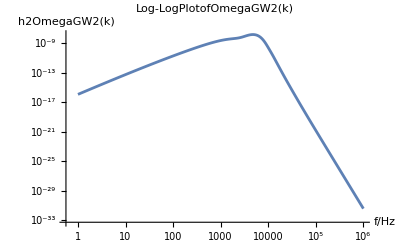

Key observation: This is the end of the GW integration script.